## Section | Non-classical light and quadratures

This chapter introduces the concept of nonclassical light, identifying quantum states of the electromagnetic field that cannot be described by classical physics. It presents several key signatures , including sub-Poissonian photon statistics, photon anti-bunching, and quadrature squeezing each indicating departures from classical behavior. The chapter explores how these features manifest in specific states like squeezed vacuum and Schrödinger-cat states, and discusses experimental techniques for generating and detecting nonclassical light, such as parametric down-conversion and homodyne detection. These tools and phenomena form the foundation for advanced applications in quantum optics, metrology, and quantum information.

#### Key concepts

Single mode quadrature squeezed states

Non-classical properties of squeezed states of light

Homodyne detection

Two-mode squeezed states

### 7.1 Quadrature squeezing

#### Squeezing definition

If two operators Â and B̂ follow the commutation relation [Â,B̂]=ⅈ Ĉ, it is a well known fact that

⟨(Δ Â)^2⟩⟨(Δ B̂)^2⟩≥1/4(|⟨Ĉ⟩|)^2

A state of a system is squeezed if one of these holds:

⟨(Δ Â)^2⟩<1/2|⟨Ĉ⟩|or⟨(Δ B̂)^2⟩<1/2|⟨Ĉ⟩|
both cannot hold otherwise uncertainty principle is violated

For quadrature operators X_1 and X_2 , the commutator is [(X̂)_1,(X̂)_2]=ⅈ/2  so quadrature squeezing exists if

⟨(Δ (X̂)_1)^2⟩<1/4 or  ⟨(Δ (X̂)_2)^2⟩<1/4

We know coherent states and the vacuum have quadrature variances of 1/4 in both quadratures, and satisfy the uncertainty inequality limit. In the figure below, we can see a representation of squeezing, in the shaded regions one quadrature variance can go below vacuum(“squeezed”) but the other one increases. Ideal squeezed states lie in the hyperbola (they satisfy the equality), but in general squeezed states can be anywhere in the shaded regions.

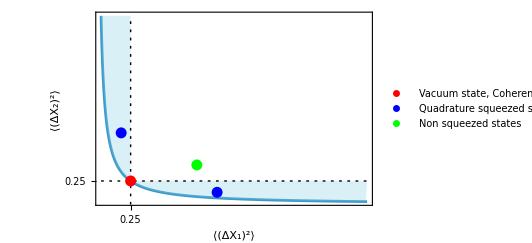

```mathematica
Legended[Show[Plot[1/(16 x),{x,1/32,2},PlotRange->Full,FrameTicks->{{{0.25},None},{{0.25},None}},Epilog->{{Dashing[{0.005,0.01}],Line[{{1/32,0.25},{2,0.25}}]},{Dashing[{0.005,0.01}],Line[{{0.25,0},{0.25,2}}]},{Red,PointSize[0.02],Point[{0.25,0.25}]},{Blue,PointSize[0.02],Point[{0.18,0.76}],Point[{0.89,0.13}]},{Green,PointSize[0.02],Point[{0.74,0.42}]}}],Graphics[{{RGBColor[0.5,0.81,0.89],Opacity[0.3],Polygon[Join[Table[{x,1/(16 x)},{x,1/32,2,0.01}],{{2,0.25},{0.25,0.25},{0.25,2}}  ]]}}],FrameLabel->(Style[#,14]&)/@{"⟨(ΔX_1)^2⟩","⟨(ΔX_2)^2⟩"},Frame->True,ImageSize->500],PointLegend[{Red,Blue,Green},{"Vacuum state, Coherent state","Quadrature squeezed states","Non squeezed states"},LegendFunction->"Panel",LabelStyle->12,LegendMarkerSize->16]]
```

A coherent is said to be the “most classical” state, and as we have seen in previous chapters it has some distinctive properties

For a coherent state with a complex amplitude α , ⟨(X̂)_1⟩_α=Re(α) and  ⟨(X̂)_2⟩=Im(α):

```mathematica
αc = RandomComplex[]
```

0.4433+0.671008 ⅈ

```mathematica
(QuantumMeasurementOperator[N[#]]@ CoherentState[][αc])["Mean"]& /@ QuadratureOperators[]
```

{0.4433,0.671008}

Check the variances correspond to the saturation point with equal variances:

```mathematica
OperatorVariance[CoherentState[][αc],#]&/@QuadratureOperators[]//RootApproximant
```

{1/4,1/4}

Phase space picture can be depicted with a circle with center (Re(α), Im(α)):

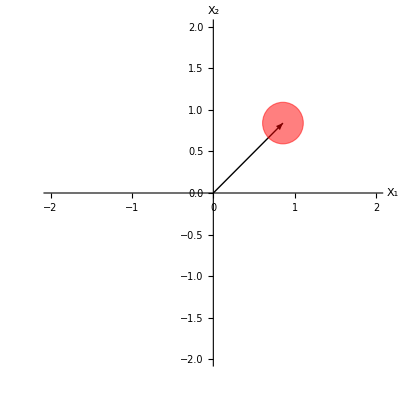

```mathematica
Graphics[
{Arrow[{{0,0},{Re[αc],Im[αc]}}],
EdgeForm[Dashed],Directive[Red],Background->LightBlue,Opacity[0.5],
Disk[{Re[αc],Im[αc]},
Chop[OperatorVariance[coherent[αc],#]&/@QuadratureOperators[]]]},
Axes->True,
AxesOrigin->{0,0},
AxesLabel->(Style[#1,14]&)/@{"X_1","X_2"},
PlotRange->{{-2,2},{-2,2}}]
```

Squeezed states are referred as non-classical , because according to the Glauber-Sudarshan P function  if one quadrature variance goes below  1/4 implies P(α) is negative in at least  some phase space region. It is also useful to introduce an angle dependent quadrature operator  X̂(θ) = 1/2(â  e^(-ⅈ θ)+(â)^† e^(ⅈ θ))

Angle dependent quadrature operator:

```mathematica
Xθ := QuantumOperator[1/2(a ⅇ^(-ⅈ θ)+SuperDagger[a] ⅇ^(ⅈ θ)),"Parameters"->θ];
```

Verify X(0) = X_1 and X(π/2) = X_2:

```mathematica
Thread[{Xθ[0] , Xθ[Pi/2]}==QuadratureOperators[]]
```

{True,True}

A squeezing  s parameter is defined s(θ) = 4⟨(ΔX(θ))^2⟩-1, squeezing exists if for some angle θ  -1 ≤ s(θ) <0:

```mathematica
sParameter[ψ_QuantumState,θ_]:= 4 OperatorVariance[ψ,Xθ[θ]]-1
```

For example, for a coherent state there are not negative values and s(θ) is identically to 0:

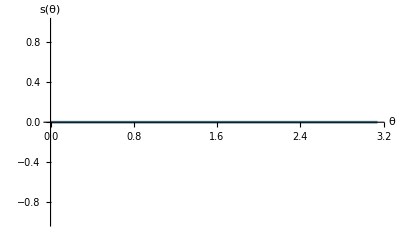

```mathematica
ListLinePlot[Chop[sParameter[CoherentState[][αc],#]&/@N@Subdivide[0,π,100]],]
```

### Squeezed operator and squeezed vacuum

The unitary squeeze operator is defined as

Ŝ(ξ)=exp(1/2(ξ^* (â)^2-ξ (â)^(†2)))

The squeeze operator can be understood as a two photon generalization of displacement operator, where ξ is a complex number ξ = r e^(ⅈ θ), r is called the squeeze parameter 0 ≤ r ≤ ∞

Quadratic combinations of â and (â)^† can generate terms like x̂ p̂+p̂ x̂, (x̂)^2, (p̂)^2 which exponentiated act like a scaling transformation. So it makes sense this operator can squeeze or stretch the variances of the quadratures

Squeeze operator in Wolfram Quantum Framework (can specify the truncation size):

```mathematica
SqueezeOperator[ξ,6]
```

QuantumOperator[…]

Representation as a single mode(qudit) operator that could potentially be included in a circuit:

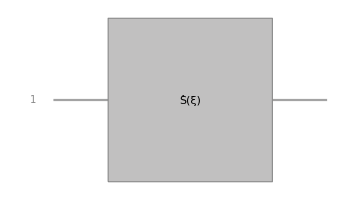

```mathematica
%["CircuitDiagram"]
```

The operator must be unitary (S(ξ))^†=S(-ξ)=S^-1(ξ):

```mathematica
FullSimplify[SuperDagger[SqueezeOperator[ξ]]-SqueezeOperator[-ξ]]//TraditionalForm
```

0

Since we are working in a truncated Fock space size, some calculations can work better numerically in a particular operator ordering:

```mathematica
SqueezeOperator[0.3,"Ordering"->"Weak"]["UnitaryQ"]
```

True

Using Baker-Hausdorff formula we can get the relations

(Ŝ)^†(ξ) â Ŝ(ξ)=â cosh(r)-(â)^† e^(ⅈ θ) sinh(r)

(Ŝ)^†(ξ) (â)^† Ŝ(ξ)=(â)^† cosh(r)-â e^(-ⅈ θ) sinh(r)

Represent the squeeze operator as a symbolic expression:

```mathematica
S[z_]:=Exp[1/2 Conjugate[z] a**a-1/2 z SuperDagger[a]**SuperDagger[a]]
```

Verify the relations, note that S^†(r ⅇ^(ⅈ θ))=S(-r ⅇ^(ⅈ θ)):

```mathematica
BosonicExpSimplify[S[-r ⅇ^(ⅈ θ)]**a**S[r ⅇ^(ⅈ θ)],Assumptions->r>0&&θ∈Reals]
```

a cosh(r)-ⅇ^(ⅈ θ) a^† sinh(r)

```mathematica
BosonicExpSimplify[S[-r ⅇ^(ⅈ θ)]**SuperDagger[a] ** S[r ⅇ^(ⅈ θ)],Assumptions->r>0&&θ∈Reals]
```

a^† cosh(r)-a ⅇ^(-ⅈ θ) sinh(r)

However, in the truncated implementation these do not hold exactly because they rely on the commutator [a,a^†] =1  , that is not exact in a truncated Fock space.
Squeeze operator is very sensitive to numerical error because it has second order terms in the annihilation and creation operators. The Fock space size has to scale  to larger sizes compared to displacement operator to get accurate numeric results

Create a squeezed vacuum state |ξ⟩=S(ξ)|0⟩:

```mathematica
ξ1 = 0.25 Exp[ⅈ 6π/13];
squeezevacuum = SqueezeOperator[ξ1][];
```

The squeeze operator does not change the expectations of X_1 and X_2:

```mathematica
(SuperDagger[squeezevacuum]@N[#]@ squeezevacuum)["Scalar"] & /@ QuadratureOperators[]
```

{0,0}

Calculating the variances:

```mathematica
Chop @ OperatorVariance[squeezevacuum,#]& /@ QuadratureOperators[]
```

{0.266204,0.297609}

We see the s-squeezing parameter does take negative values:

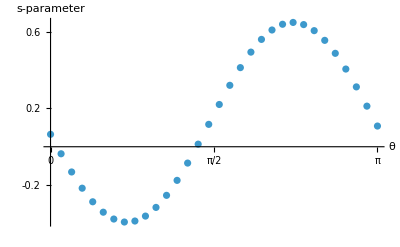

```mathematica
ListPlot[Table[Re[sParameter[squeezevacuum,β]],{β,0,π,0.1}],]
```

Why one of the variances is not going below 0.25?

Using the properties of Ŝ on a and a^† can be derived that

⟨Δ X_1⟩^2=1/4[(cosh(r))^2+(sinh(r))^2-2sinh(r)cosh(r)cos(θ)]

⟨Δ X_2⟩^2=1/4[(cosh(r))^2+(sinh(r))^2+2sinh(r)cosh(r)cos(θ)]

Verification:

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},Table[1/4(Cosh[r]^2+Sinh[r]^2-(-1)^m 2Sinh[r]Cosh[r]Cos[θ]),{m,0,1}]]
```

{0.266204,0.297609}

When θ=0 the expressions reduce to ⟨Δ X_1⟩^2=1/4 e^(-2r)  and ⟨Δ X_2⟩^2=1/4 e^(2r) .
For this case we can clearly see one quadrature gets “squeezed” while the other increases so it maintains the uncertainty principle. For the case (θ = 0)  the inequality is saturated ( the product of uncertainties equals 1/16 = 0.0625). This is different from a coherent state or the vacuum that also saturate the inequality, but with the same value of the uncertainties in X_1 and X_2.

Set up ξ as a real parameter:

```mathematica
ξ1 = RandomReal[{0,0.6}];
squeezevacuum = SqueezeOperator[ξ1][];
```

Calculate the variances, this time we do get one below 0.25:

```mathematica
variances = (OperatorVariance[squeezevacuum,#]//Chop)& /@ QuadratureOperators[]
```

{0.121572,0.514099}

That coincide with the exponential expressions:

```mathematica
1/4{Exp[-2ξ1],Exp[2ξ1]}
```

{0.121572,0.5141}

Phase space representation for the cases  θ = 0 and θ=π (not to scale for visual purposes). In these cases the squeezing is along the axes of X_1 or X_2 describing error ellipses:

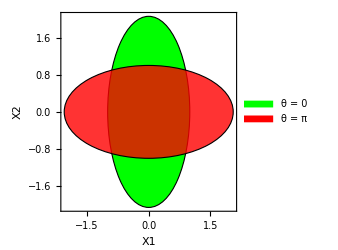

```mathematica
With[{dx =1, dy =variances[[2]]/variances[[1]]//Log}, 
Legended[
Graphics[{
EdgeForm[Dashed],Green,Disk[{0,0},{dx,dy}],
Opacity[0.8],Red,Disk[{0,0},{dy,dx}]},
Axes->True,
Frame->True,
ImageSize->250,
AxesLabel->{"X1","X2"}],
SwatchLegend[{Green,Red},{"θ = 0", "θ = π"}]]]
```

For a general  ξ = r e^ⅈθ we can define rotated quadrature operators Y_1 = cos(θ/2)X_1+ sin(θ/2)X_2  and Y_2= -sin(θ/2)X_1+cos(θ/2)X_2 such that the variances are calculated along the rotated quadrature axes. For these operators  the variances are  ⟨Δ Y_1 ⟩^2 = 1/4 e^(-2r),  ⟨Δ Y_2 ⟩^2 = 1/4 e^(2r) .  At  θ = 0, Y_1 and Y_2 reduce to X_1 and X_2

Rotated quadrature operators:

```mathematica
YOperators :=( QuantumOperator[#,"Parameters"->θ]& )/@( RotationMatrix[-θ/2].QuadratureOperators[])
```

Setting θ = 0 reduce to the original quadratures:

```mathematica
Through[YOperators[0]] == QuadratureOperators[]
```

True

Squeezed vacuum:

```mathematica
ξ1 = RandomComplex[{0,0.5 ⅇ^(ⅈ π/4)}];
squeezevacuum = SqueezeOperator[ξ1][];
```

Now we do get one quadrature below 0.25:

```mathematica
variances = With[{r = Abs[ξ1], θ1 = Arg[ξ1]}, OperatorVariance[squeezevacuum,#]& /@ Through[YOperators[θ1]]]//Chop
```

{0.150472,0.415359}

That also coincides with the exponential forms as before:

```mathematica
1/4{Exp[-2r],Exp[2r]}/. r->Abs[ξ1]
```

{0.150472,0.415359}

So the plot that was shown in the previous section was not the full story, some states can be quadrature squeezed when you measure them in the right squeezing axis

Phase space picture are rotated ellipses with angle of rotation θ/2  (the dashed lines represent the Y_1 and Y_2 quadrature axes)

### 7.2 Squeezed states and its properties

#### Squeezed coherent state and displaced squeezed state

A squeezed coherent state is obtained applying the squeeze operator to a coherent state

|ξ,α⟩=Ŝ(ξ)|α⟩=Ŝ(ξ)D̂(α)|0⟩

Let’s use a bigger truncation size:

```mathematica
SetFockSpaceSize[80];
```

Set up complex amplitudes, the following values are chosen for visualization purposes:

```mathematica
{αcoh,ξ1}={3.2,0.6 ⅇ^(ⅈ π/4)};
```

Build a squeezed coherent state:

```mathematica
squeezeCoh = SqueezeOperator[ξ1]@ CoherentState[][αcoh];
```

Mean number of photons has the following analytical expression

⟨n̂⟩=(|α|)^2((cosh(r))^2+(sinh(r))^2)-(α^*)^2 e^(ⅈ θ) sinh(r)cosh(r)
-α^2 e^(-ⅈ θ)sinh(r)cosh(r)+(sinh(r))^2

Visualize the photon distributions of the coherent state and the resulting squeezed coherent state:

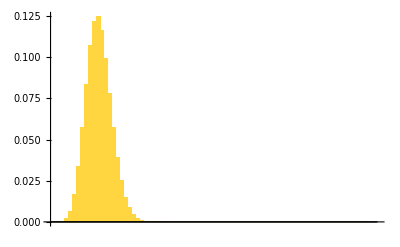
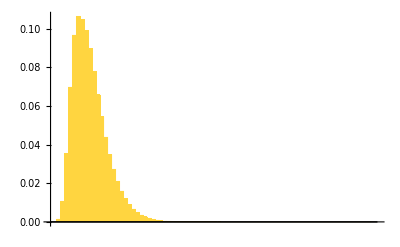
-Graphics--Graphics-Photon distributions of |α⟩ and S(ξ)|α⟩

```mathematica
Labeled[Row[#["ProbabilitiesPlot",ChartLabels->None]&/@{CoherentState[][αcoh],squeezeCoh}],"Photon distributions of |α⟩ and S(ξ)|α⟩",Top]
```

Mean number of photons from QuantumMeasurementOperator:

```mathematica
(QuantumMeasurementOperator[SuperDagger[a]@a]@squeezeCoh)["Mean"]
```

8.01677

Compare with the analytical expression:

```mathematica
With[{r=Abs[ξ1],θ=Arg[ξ1]},Abs[αcoh]^2 (Cosh[r]^2+Sinh[r]^2)+Sinh[r]^2-2 Re[αcoh^2 Exp[-ⅈ θ]] Cosh[r] Sinh[r]]
```

8.01677

Another state  that is more general than the squeezed vacuum is the displaced squeezed state is defined as: |α, ξ ⟩ =  D(α) S(ξ)|0⟩, is not the same as a squeezed coherent state because the displacement operator and the squeeze operator do not commute

Clearly the commutator is not 0, plotting the matrix of the resulting operator:

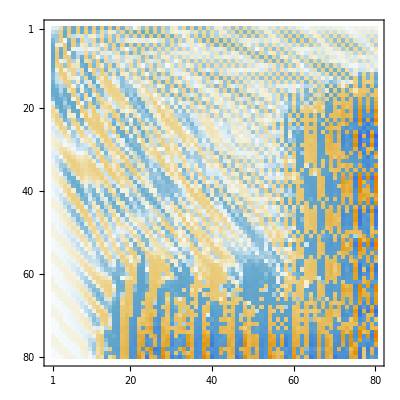

```mathematica
Commutator[SqueezeOperator[ξ1],DisplacementOperator[αcoh]]["Matrix"]//MatrixPlot
```

For a displaced squeezed state the mean number of photons is

⟨n̂⟩=(|α|)^2+(sinh(r))^2

When r->0 the results for a coherent state are recovered, or when α → 0  the results of squeezed vacuum are recovered

Displaced squeezed state:

```mathematica
dispSqueezed = DisplacementOperator[αcoh]@ SqueezeOperator[ξ1][];
```

Mean number of photons comparison:

```mathematica
{(QuantumMeasurementOperator[SuperDagger[a]@a]@ dispSqueezed)["Mean"],Abs[αcoh]^2 +Sinh[Abs[ξ1]]^2}
```

{10.6453,10.6453}

For this state it still holds ⟨(Δ Y_1)^2⟩=1/4 e^(-2r), ⟨(Δ Y_2)^2⟩=1/4 e^(2r)
That can be interpreted that the error ellipses keep their shape for any ξ, the center is displaced by α maintaining the ellipse shape

Variance calculation:

```mathematica
With[{r = Abs[ξ1], θ1 = Arg[ξ1]}, {OperatorVariance[dispSqueezed,#]& /@ Through[YOperators[θ1]]//Chop,1/4{Exp[-2r],Exp[2r]}}]
```

{{0.0752986,0.830029},{0.0752986,0.830029}}

Phase space representation of the error ellipse:

```mathematica
Module[{θ1=Arg[ξ1],dx ,dy, h=Re[αcoh], k = Im[αcoh]}, 
dx = OperatorVariance[dispSqueezed,YOperators[[1]][θ1]];dy =OperatorVariance[dispSqueezed,YOperators[[2]][θ1]] ;Graphics[{EdgeForm[Thick],Green,
Rotate[Disk[{h,k},{dx,dy}],θ1/2],
Black,Dashed,Line[#+{h,k}&/@Outer[Times,{-dx,dx},{Cos[θ1/2],Sin[θ1/2]}]],Line[#+{h,k}& /@ Outer[Times,{-dy,dy},{-Sin[θ1/2],Cos[θ1/2]}]
],PointSize[0.022],Point[{h,k}],{Red,Dashing[1,0,0],Arrow[{{0,0},{h,k}}],Text["α",{0.24*h,0}+{h,k}/2]}},
Axes->True,Frame->True,ImageSize->Medium,FrameLabel->{"X1","X2"},PlotRange->{{0,6},{-1.5,1.5}},AspectRatio->0.6,ImageSize->400]
]
```

-Graphics-

We would get a very similar plot using the Wigner function:

```mathematica
wigner = WignerRepresentation[dispSqueezed,{0,6},{-4,4},"GridSize"->50,"GaussianScaling"->2];
```

Plot the function:

```mathematica
DensityPlot[wigner[x,p],{x,0,6},{p,-4,4},]
```

-Graphics-

#### Properties of a squeezed vacuum state

For a squeezed vacuum state it can be shown mathematically that  the photon distribution only has non zero values for states with even number of photons

|ξ⟩=1/(√(cosh(r)))∑_(m=0)^∞ (-1)^m(√((2m)!))/(2^m m!)e^(ⅈ m θ)(tanh(r))^m|2m⟩

```mathematica
SetFockSpaceSize[41];
```

Random amplitude:

```mathematica
ξ1 = RandomReal[{1,2}]Exp[ⅈ RandomReal[{0,2Pi}]];
```

Squeezed vacuum:

```mathematica
sv = SqueezeOperator[ξ1][];
```

See the photon distribution:

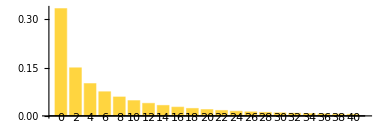

```mathematica
sv["ProbabilityPlot",AspectRatio->1/3]
```

Analytical Fock basis expansion:

```mathematica
amps =With[{vals = AbsArg[ξ1]}, 1/(√Cosh[vals[[1]]])Table[((-1)^m √((2 m)!) ⅇ^(ⅈ m vals⟦2⟧) tanh^m(vals⟦1⟧))/(2^m m!),{m,0,Ceiling[$FockSize/2-1]}]];
```

Check amplitudes equality:

```mathematica
Chop[amps -sv["AmplitudeList"]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The squeezed vacuum satisfies the Bogoliubov transformation eigenvalue equation

(â cosh(r)+e^(ⅈ θ)(â)^†sinh(r))|ξ⟩=0

Define the linear combination of creation and annihilation operators:

```mathematica
op =(a Cosh[Abs[ξ1]] + ⅇ^(ⅈ Arg[ξ1]) SuperDagger[a] Sinh[Abs[ξ1]]);
```

Indeed the squeezed state is an eigenstate with eigenvalue 0:

```mathematica
Chop[op@sv]
```

0

### 7.3 Generation of squeezed states

A common technique  to generate squeezed light is  to implement parametric processes with the aid of non linear optical devices. A non-linear medium  is pumped by a field of frequency ω_P,  and photons of the field are converted into pairs of signal photons each of frequency ω = ω_P/2. This is known as degenerate parametric down-conversion

Can be represented by this Hamiltonian

Ĥ=ℏ ω (â)^†â+ℏ ω_P(b̂)^†b̂-ⅈ ℏ χ^(2)((â)^2(b̂)^†-(â)^(†2)b̂)

where  b is the pump mode, a is the signal mode and χ^(2) is the second order susceptibility

And we can make the approximation that the pump is a really strong classical field, strong enough to never run out of photons. We can assume the field  is in  a coherent state |β e^(- ⅈ ω_P t)⟩ and operator b and b^† are replaced by  β e^(- ⅈ ω_P t) and β^* e^(ⅈ ω_P t), so the Hamiltonian can be expressed as:

(Ĥ)^(PA)=ℏ ω (â)^†â+ⅈ ℏ (η^*(â)^2 e^(ⅈ ω_P t)-η (â)^(†2)e^(-ⅈ ω_P t)) where η=β χ^(2)

Set the truncation size:

```mathematica
SetFockSpaceSize[40];
```

Time independent term:

```mathematica
H0PA = h ω SuperDagger[a]@a;
```

Time dependent term:

```mathematica
HIPA = ⅈ h (η* a@a ⅇ^(ⅈ Subscript[ω, P] t)-η  (SuperDagger[a]@SuperDagger[a] ⅇ^(-ⅈ Subscript[ω, P] t)));
```

Exponential of free part:

```mathematica
U0 =  MatrixExp[-ⅈ H0PA/h t];
```

Going to the interaction picture:

```mathematica
HI = QuantumOperator[Simplify[SuperDagger[U0]@ HIPA @ U0,Element[{h,Subscript[ω, P],t,ω},Reals]],"Parameters"->{Subscript[ω, P],ω,η}];
```

We get an interaction picture Hamiltonian that is time dependent , but when we consider ω_P = 2 ω that is an energy conservation condition , then the Hamiltonian becomes time independent

```mathematica
FreeQ[HI[ωp,ω]["Amplitudes"]//Values,t]
```

False

```mathematica
FreeQ[HI[2ω,ω]["Amplitudes"]//Values,t]
```

True

The evolution operator using this interaction Hamiltonian can be shown to take the form of a squeeze operator where ξ = 2 η t, which should not come as a surprise because of the (â)^2 and (â)^(†2) terms.

We can check comparing the Frobenius norm of || U - SqueezeOperator(||)_F numerically , for the sake of the example we take η=1. The evolution operator has good agreement to the SqueezeOperator with “Weak” ordering because of the form of interaction Hamiltonian:

```mathematica
Table[Norm[
(MatrixExp[-ⅈ HI[2ω,ω,1]t/h]-SqueezeOperator[2 t,"Ordering"->"Weak"])["Matrix"],"Frobenius"],{t,0.1,0.5,0.05}]
```

{2.27714×10^-15,2.73831×10^-15,3.52088×10^-15,1.45693×10^-14,4.21401×10^-15,5.32617×10^-15,5.47962×10^-15,7.7197×10^-15,2.24455×10^-14}

But not with the default normal order:

```mathematica
Table[Norm[
(MatrixExp[-ⅈ HI[2ω,ω,1]t/h]-SqueezeOperator[2 t])["Matrix"],"Frobenius"],{t,0.1,0.5,0.05}]
```

{1.98314,2.49976,2.92302,3.28608,3.60666,3.89497,4.156,4.39125,4.59986}

Normal ordered calculations are more robust numerically in truncated spaces. So the matrix elements of the operators in weak and normal ordering can have significant differences due to truncation

Visualize the difference for ξ=0.2:

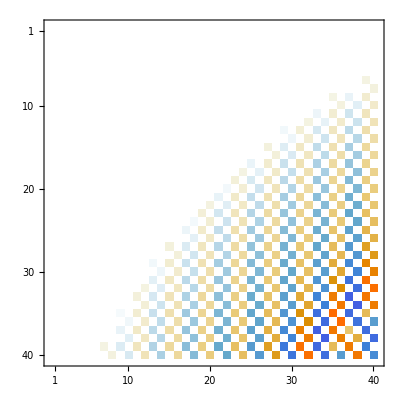

```mathematica
MatrixPlot[Chop[(SqueezeOperator[0.2,"Ordering"->"Weak"]-SqueezeOperator[0.2])["Matrix"]]]
```

That does not mean that we do not have matrix elements with good accuracy in both cases, for example when applying to the vacuum:

```mathematica
With[{state =MatrixExp[-ⅈ HI[2ω,ω,1]0.5/h][]},Table[QuantumSimilarity[state,SqueezeOperator[2 0.5,"Ordering"->ord][]],{ord,{"Normal","Weak"}}]]
```

{0.999997,1.}

### 7.4 Detection of squeezed state : Balanced Homodyne detection

A balanced beam splitter with the signal in port 1 and the local oscillator in port 2 sends the difference of the two detector photocurrents to

i_34=(n̂)_3-(n̂)_4=((â)_3)^†(â)_3-((â)_4)^†(â)_4=ⅈ (((â)_2)^†(â)_1-((â)_1)^†a_2)

Given an input state where |β⟩ is a coherent state and ψ any state :

|in⟩=|ψ⟩_1|β⟩_2

We get for the current:

⟨(n̂)_3-(n̂)_4⟩=⟨i_34⟩=2 |β|⟨in|X(ϕ-π/2)|in⟩

Where ϕ is the phase of the complex  number β. We can define θ = ϕ - π/2 and the quadrature at angle θ is defined X(θ)=1/2(â e^(-ⅈ θ)+(â)^†e^(ⅈ θ)), to vary θ we vary ϕ and get different quadrature measurements

Also for that kind of input state each expectation factorizes

⟨a_2^†a_1⟩ = ⟨a_2^†⟩_β⟨a_1⟩_ψ = β* ⟨a⟩_ψ  and similarly ⟨a_1^†a_2⟩=β ⟨a(⟩*)_ψ

Then an alternative calculation is:

⟨(î)_34⟩=-2|β|Im[ⅇ^(ⅈ ϕ)⟨a⟩_ψ]

For the second moments we get a similar formula

⟨(Δ(i_34))^2⟩=4 |β|^2⟨(Δ X(θ))^2⟩

Set the truncation size:

```mathematica
SetFockSpaceSize[40];
```

Mode operators:

```mathematica
{a1,a2}=Array[AnnihilationOperator[{#}]&,2];
nOp = SuperDagger[a1]@a1;
```

Photo-current difference definition:

```mathematica
i34 =ⅈ(SuperDagger[a2]@a1-SuperDagger[a1]@a2);
```

Expectation value helper:

```mathematica
expect[qs_,op_]:=(SuperDagger[qs]@(op@qs))["Scalar"];
```

Quadrature at angle θ:

```mathematica
X[θ_]:=1/2 (Exp[-ⅈ θ] a+Exp[ⅈ θ] SuperDagger[a])
```

List of values of ϕ:

```mathematica
phis=N@Subdivide[0,2 Pi,40];
```

Define two signals: a coherent state, which is the shot-noise reference, and the displaced squeezed state that the section is about

Set up parameter values:

```mathematica
α0=0.6+0.25 I;
ξ0=0.5 Exp[I 0.7];
```

Define the states:

```mathematica
psiCoh=CoherentState[][α0];
psiSq=DisplacementOperator[α0]@SqueezeOperator[ξ0][];
```

Assuming a local oscillator | β |= 3, calculate ⟨i_34⟩ with the two mode definition:

```mathematica
refVals=Table[Chop[expect[QuantumTensorProduct[psiSq,CoherentState[][3. Exp[I ϕ]]],i34]/(2 3.)],{ϕ,phis}];
```

And with the alternative way:

```mathematica
fast=With[{a0=expect[psiSq,a]},-Im[Exp[-I #] a0]&/@phis];
```

Verify they are numerically the same:

```mathematica
Max@Abs[refVals-fast]
```

6.52811×10^-14

Plot the result:

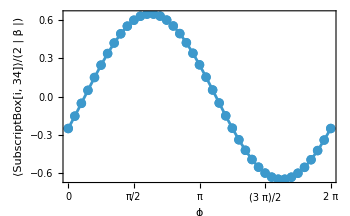

```mathematica
ListLinePlot[Transpose[{phis,fast}],]
```

For a coherent state we can extract the parameters easily, X(ϕ = 0) = X(θ = –π/2) = -X_2 , and X(ϕ = π/2) = X(θ = 0) = X_1 so the real and imaginary part of the α amplitude can be obtained

```mathematica
{X[0]==QuadratureOperators[][[1]],X[π/2]==QuadratureOperators[][[2]]}
```

{True,True}

Information about the imaginary part:

```mathematica
{Im[α0],-fast[[1]]}
```

{0.25,0.25}

Information about the real part:

```mathematica
{Re[α0],fast[[Ceiling[(Length@fast/4)]]]}
```

{0.6,0.6}

Photo-current curve:

```mathematica
curve[qs_]:=Table[Re@Chop@expect[QuantumTensorProduct[qs,CoherentState[][3. Exp[I ϕ]]],i34]/(2*3.),{ϕ,phis}];
```

Compare the curves with and without squeezing:

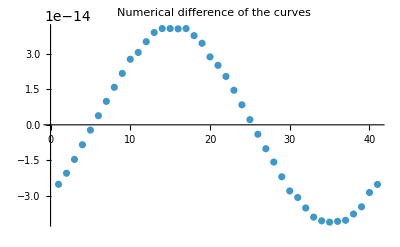

```mathematica
ListPlot[curve[psiCoh]-curve[psiSq],PlotLabel->"Numerical difference of the curves"]
```

```mathematica
{Re[expect[#,nOp]&/@{psiCoh,psiSq}],Re@Chop@OperatorVariance[#,X[0]]&/@{psiCoh,psiSq}}
```

{{0.4225,0.69404},{0.25,0.161059}}

The curves coincide while the photon numbers differ by 64% and the quadrature variances by a third. The mean photo-current cannot see squeezing at all , it sees one complex number and the displaced squeezed signal keeps its squeezing entirely in moments the mean discards. That is why the measurement has to go to second order moments.

The reference is the coherent state, that has a an isotropic covariance matrix, but that changes with the squeezing:

```mathematica
{covCoh,covSq} = Chop@CovarianceMatrix[#,"QuadratureScaling"->1/2]&/@{psiCoh,psiSq}
```

{{{0.25,0},{0,0.25}},{{0.161059,-0.189271},{-0.189271,0.610481}}}

The squeezed signal breaks the isotropy, and its variance curve can be computed as a quadratic form that depends on the covariance matrix

V(θ)= u^T(θ) σ  u(θ),   u(θ)={cos(θ), sin(θ)}

We will say more about covariance matrices in section 7.7

Check the claim:

```mathematica
quadForm[s_,t_]:={Cos[t],Sin[t]}.s.{Cos[t],Sin[t]};
Table[{t,Re@Chop@OperatorVariance[psiSq,X[t]],quadForm[covSq,t]},{t,0,π,π/6}]//Column
```

{0,0.161059,0.161059}
{π/6,0.109501,0.109501}
{π/3,0.334212,0.334212}
{π/2,0.610481,0.610481}
{(2 π)/3,0.662039,0.662039}
{(5 π)/6,0.437329,0.437329}
{π,0.161059,0.161059}

The curve dips to a third of shot noise in one direction and pays for it with two and a half times shot noise in the other approximately:

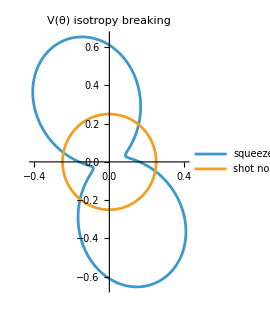

```mathematica
PolarPlot[{quadForm[covSq,θ],quadForm[covCoh,θ]},{θ,0,2 Pi},]
```

Compute the extrema numerically:

```mathematica
#[{quadForm[covSq,θ],0<θ<π},θ]&/@{NMaximize,NMinimize}
```

(0.67957 | {θ→1.9208}
0.0919699 | {θ→0.35})

Both quantities were moments, a homodyne run returns a number per shot. And the histogram of those numbers is the quadrature probability density. The eigenstates of X(θ) are rotations of the |x⟩_θ=ⅇ^(ⅈ θ n̂)|x⟩. So the amplitude is the phase weighted sum Pr(x, θ)=|∑_n c_n ⅇ^(-ⅈ n θ)φ_n(x)|^2 where φ_n are the harmonic oscillator wave-functions

Define the quadrature density:

```mathematica
quadratureDensity[qs_]:=Module[{n=Range[0,$FockSize-1],coef},coef=(qs["AmplitudesList"] (2/π)^(1/4))/(√(2^n n!));Abs[coef.(Exp[-ⅈ n #2-#1^2] HermiteH[n,√2 #1])]^2&]
```

Compute the density for the states:

```mathematica
densities = quadratureDensity/@{psiCoh,psiSq};
```

Visualize the plot of the densities in the x-θ plane:

```mathematica
GraphicsRow[DensityPlot[#[x,θ],{θ,0,2 Pi},{x,-3,3},]&/@densities]
```

-Graphics-

The coherent band has constant width, while the squeezed band distorts pinching to its narrowest at θ_s and bulging a quarter turn later, while both centers trace the same sinusoid curve

The closing calculation fits r and the squeezing angle from the variance curve

Helper for simulating a measurement of variance V(θ):

```mathematica
vMeas[qs_,amp_,θ_]:=With[{st=QuantumTensorProduct[qs,CoherentState[][amp Exp[ⅈ (θ+π/2)]]]},With[{m=expect[st,i34]},Re[expect[st,i34^2]-m^2]/(4 amp^2)]]
```

Mean number of photons of the squeezed state:

```mathematica
nbarSq=Re@expect[psiSq,nOp]
```

Get the simulated data, comparing the ideal case to the case representing the effect of the local-oscillator in the homodyne detection:

```mathematica
{dataIdeal,dataMeas}=With[{ths=N[Subdivide[0,2 π,24]]},Transpose[Table[{{t,quadForm[covSq,t]},{t,vMeas[psiSq,3.,t]}},{t,ths}]]];//Quiet
```

V(θ) can be represented with the following model, that comes from analytical calculations:

```mathematica
model=1/4 (Exp[-2 r] Cos[θ-θ0/2]^2+Exp[2 r] Sin[θ-θ0/2]^2)
```

1/4 (ⅇ^(2 r) sin^2(θ-θ0/2)+ⅇ^(-2 r) cos^2(θ-θ0/2))

Fit the data to the model:

```mathematica
fit =NonlinearModelFit[dataMeas,model,{{r,0.3},{θ0,0.2}},θ]["BestFitParameters"]
```

{r→0.517456,θ0→0.703403}

There is a higher error in the squeezing parameter r :

```mathematica
PercentForm[Abs[AbsArg[ξ0]-{r,θ0}/. fit]/AbsArg[ξ0]]
```

{3.491%,0.4862%}

Compare graphically the ideal curve with simulated homodyne results:

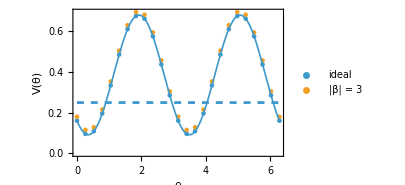

```mathematica
Show[ListPlot[{dataIdeal,dataMeas},PlotLegends->{"ideal","|β| = 3"}],]
```

### 7.5 Schrodinger cat states

Another important type of states with non-classical properties are superpositions of classical-like states.  Let’s analyze the superposition of coherent states with equal amplitude magnitude but with a phase difference of π (α and -α)  so the state has the form

|ψ⟩=𝒩(|α⟩+e^(ⅈ ϕ)|-α⟩)  where 𝒩 is a normalization factor , ϕ relative phase

When |α| is large the states are macroscopically distinguishable  and the superpositions are called Schrodinger cat states( resembling the dead or alive state), Schrodinger’s intention was to mock the Copenhagen interpretation of quantum mechanics. Nowadays, it is possible to consider quantum superpositions of macroscopically distinguishable states in an experimental setup. The reason of why we do not observe superpositions of macroscopic states naturally, is because a quantum system is not  completely isolated,  it interacts with the environment and as a result quantum superpositions decohere into statistical mixtures. The state decays into a statistical mixture of the form  ρ̂=(|β⟩⟨β|+|-β⟩⟨-β|)/2, and when |α| is big that decay is faster, for now we will focus on the non-classical properties of these states.

Based on the general definition of a Schrodinger cat state, setting ϕ = 0 yields a state called even cat state, while setting ϕ = π results in an odd cat state. The case when ϕ = π/2 is known as the Yurke-Stoler state. Notably, all three of these states are eigenstates of (â)^2 with eigenvalue α^2

```mathematica
SetFockSpaceSize[21];
```

Lets visualize the photon distributions, the even cat state only has non zero amplitudes at even Fock states:

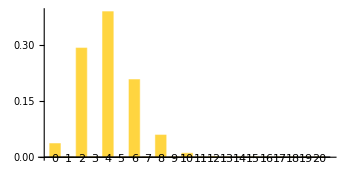

```mathematica
CatState[][2.,0]["ProbabilitiesPlot",AspectRatio->1/2]
```

We see applying the a^2 to the state recovers the same state:

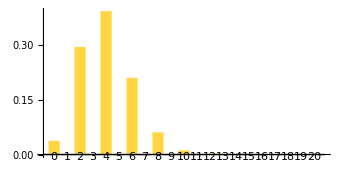

```mathematica
(a^2)[CatState[][2.,0]]["ProbabilitiesPlot",AspectRatio->1/2]
```

```mathematica
With[{s=CatState[][2.,0]},QuantumSimilarity[(a^2)[s]["Normalize"],s]]
```

1.

Odd cat state only has non-zero amplitudes at odd photon Fock states:

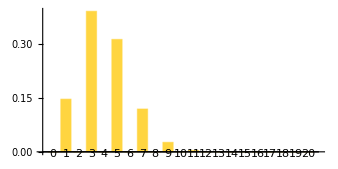

```mathematica
CatState[][2.,π]["ProbabilitiesPlot",AspectRatio->1/2]
```

For Yurke-Stoler the distribution is identical of a coherent state |α⟩, the amplitudes are not the same though:

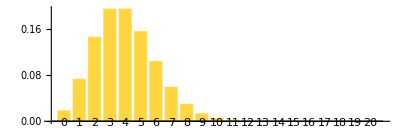

```mathematica
CatState[][2.,π/2]["ProbabilityPlot",AspectRatio->1/3]
```

Equal probabilities:

```mathematica
Chop[CatState[][2.,π/2]["ProbabilityList"]-CoherentState[][2.]["ProbabilityList"]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Ratio of amplitudes there is a phase ⅇ^(± ⅈ π /4) for each amplitude, so is not a global phase:

```mathematica
RootApproximant[Arg[Chop[CatState[][2.,π/2]["AmplitudeList"]/CoherentState[][2.]["AmplitudeList"]]]/π]
```

{1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4}

There is also the concept of amplitude or number squeezing that comes from the uncertainty relation [n,φ] = ⅈ, a simple quantity that gives information about the photon statistics is the Mandel Q-parameter Q=(⟨(Δn)^2⟩-⟨n⟩)/⟨n⟩. For a state with -1 ≤ Q<0 the statistics are sub-Poissonian, if Q > 0 super-Poissonian and Q=0 corresponds to Poissonian statistics

The Mandel Q-parameter for even cat state is > 0 so has super-Poissonian statistics for all α, for the odd cat state is < 0 for all α  showing sub-Poissonian statistics. For the Yurke-Stoler state  obviously Q = 0 because its photon distribution is the same as coherent state, when |α| is large  Q → 0 for both even and odd cat states.

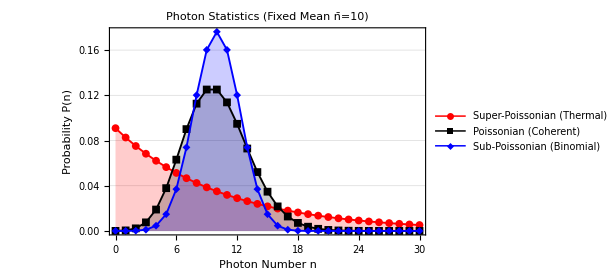

Define Mandel Q-parameter:

```mathematica
MandelQParameter[ψ_QuantumState]:= With[{mean=(ψ["Dagger"]@SuperDagger[a]@a@ψ)["Scalar"]},(OperatorVariance[ψ,SuperDagger[a]@a]- mean)/mean]
```

Calculate the parameter for even cat state, Yurke-Stoler and odd cat state, varying α:

```mathematica
Table[MandelQParameter@CatState[][αc,ϕ],{αc,{0.2,0.5,1.,1.5}},{ϕ,{0,π/2,π}}]//Chop
```

{{0.998934,0,-0.998934},{0.959517,0,-0.959517},{0.551441,0,-0.551441},{0.0999933,0,-0.0999933}}

Even cat states and Yorke-Stoler states present quadrature squeezing (this holds for any α real)

Random α:

```mathematica
αc = RandomReal[{0,2}];
```

Quadratures variances for the states:

```mathematica
TableForm[Table[With[{val=Chop@OperatorVariance[CatState[][αc,ϕ],quad]},If[val<0.25,Highlighted[val],val]],{ϕ,{0,π,π/2}},{quad,QuadratureOperators[]}],TableHeadings->]
```

| X_1 | X_2
Even cat | 0.520422 | 0.126906
Odd cat | 0.972305 | 0.578788
Yorke-Stoler | 0.643516 | 0.168463

For the mixture

ρ̂=1/2(|α⟩⟨α|+|-α⟩⟨-α|)

⟨(Δ X_1)^2⟩=1/4+α^2 and ⟨(Δ X_2)^2⟩=1/4 , so there is clearly not squeezing

For example for α = 2, define the statistical mixture:

```mathematica
statisticalMixture = 1/2CoherentState[][2.]["MatrixState"]+1/2CoherentState[][-2.]["MatrixState"];
```

Quadrature variances:

```mathematica
With[{m =statisticalMixture["Operator"]}, Tr[(#@#)@m]- Tr[#@m]^2& /@ QuadratureOperators[]]//Chop
```

{4.25,0.25}

The Wigner quasi-probability distribution can give more insight about the contrast of  superpositions and statistical mixtures. The Wigner function for the statistical mixture are two gaussian peaks centered at ± α (or scalings of it) . The Wigner function of the even cat state shows a behavior that is oscillatory because of the interference of |α⟩ and |-α⟩, and also presents negative values that is a non-classical characteristic. The Wigner functions for the odd cat state and Yorke-Stoler are quite similar in behavior to the even cat state.

Wigner function of even cat state:

```mathematica
Block[{wig = WignerRepresentation[CatState[][2,0],{-4.5,4.5},{-4.5,4.5}]},
Plot3D[wig[x,p],{x,-4.5,4.5},{p,-4.5,4.5},
]]
```

-Graphics3D-

Wigner function of statistical mixture:

```mathematica
Block[{wig = WignerRepresentation[statisticalMixture,{-4.5,4.5},{-4.5,4.5}]},
Plot3D[wig[x,p],{x,-4.5,4.5},{p,-4.5,4.5},
]]
```

-Graphics3D-

### 7.6 Two-mode squeezing

We now consider squeezing with multimode fields, this means it is possible to have entanglement between the modes , such characteristics can exhibit more diverse non-classical effects. We will just explore the two mode case , defining the two mode squeeze operator and two mode squeezed vacuum:

(Ŝ)_2(ξ)=exp(ξ^* â b̂-ξ (â)^† (b̂)^†)

|ξ⟩_2=(Ŝ)_2(ξ)|0,0⟩

Similar to the expressions we obtained for the single mode ladder operators, we can get the following transformations using two modes:

((Ŝ)_2(ξ))^†(â)_1(Ŝ)_2(ξ)=cosh(r)(â)_1-ⅇ^(ⅈ θ)sinh(r)(â)_2^†
((Ŝ)_2(ξ))^†(â)_1^†(Ŝ)_2(ξ)=cosh(r)(â)_1^†-ⅇ^(-ⅈ θ)sinh(r)(â)_2
((Ŝ)_2(ξ))^†(â)_2(Ŝ)_2(ξ)=cosh(r)(â)_2-ⅇ^(ⅈ θ)sinh(r)(â)_1^†
((Ŝ)_2(ξ))^†(â)_2^†(Ŝ)_2(ξ)=cosh(r)(â)_2^†-ⅇ^(-ⅈ θ)sinh(r)(â)_1

Define the symbolic two mode squeezing operator:

```mathematica
S2[ξ_]:= Exp[ξ* a1**a2-ξ SuperDagger[a1]**SuperDagger[a2] ]
```

Use BosonicExpSimplify for reduction of the expressions S_2(-ξ)[.]S_2(ξ):

```mathematica
red =BosonicExpSimplify[S2[-r ⅇ^(ⅈ θ)]**#**S2[r ⅇ^(ⅈ θ)],Assumptions->θ∈Reals && r>0]&;
```

Display the obtained expressions:

```mathematica
TraditionalForm[formattedExpr@*red/@FieldVariables[{1,2}]//Column]
```

cosh(r) a1-ⅇ^(ⅈ θ) sinh(r) a2^†
cosh(r) a1^†-ⅇ^(-ⅈ θ) sinh(r) a2
cosh(r) a2-ⅇ^(ⅈ θ) sinh(r) a1^†
cosh(r) a2^†-ⅇ^(-ⅈ θ) sinh(r) a1

Note the squeezed operator of two modes cannot be decomposed as a product of two single mode squeeze operator, so it makes sense this operator produces entangled squeezed states with correlations between the two modes

```mathematica
SetFockSpaceSize[30];
```

Operators for each mode:

```mathematica
{a1,b1}= Array[AnnihilationOperator[{#}]&,2];
```

One direct way to simultaneously apply an operator to two modes is to use the “Bend” property:

```mathematica
a1["Bend"] == a1@b1
```

True

Test with creation operator:

```mathematica
SuperDagger[a1]["Bend"][FockState[{0,0}]]//TraditionalForm
```

11

Two mode squeeze vacuum definition:

```mathematica
twoModesqueezeVacuum[ξ_?NumberQ]:= MatrixExp[(ξ* a1["Bend"]-ξ SuperDagger[a1]["Bend"]),FockState[{0,0}]]
```

We can define quadrature operators for the two mode field:

X_(1  two mode)=1/2^(3/2)((â)_1+((â)_1)^†+(b̂)_1+((b̂)_1)^†)

X_(2 two mode)=1/(2^(3/2)ⅈ)((â)_1-((â)_1)^†+(b̂)_1-((b̂)_1)^†)

Defining them in terms of quantum operators:

```mathematica
twomodeX1 := 1/2^(3/2)(a1+SuperDagger[a1]+b1+SuperDagger[b1])
twomodeX2 := 1/(2^(3/2) ⅈ)(a1-SuperDagger[a1]+b1-SuperDagger[b1])
```

Check the commutator is still ⅈ/2 for the two mode definition:

```mathematica
BosonicNormalOrder[Commutator[
1/2^(3/2)(a+SuperDagger[a]+b+SuperDagger[b]),1/(2^(3/2) ⅈ)(a-SuperDagger[a]+b-SuperDagger[b])],
FieldVariables[{a,b}]]
```

ⅈ/2

It holds that  ⟨X_1⟩ = ⟨X_2⟩ = 0:

```mathematica
ξ1 = RandomComplex[];
With[{state = twoModesqueezeVacuum[ξ1]}, (SuperDagger[state]@ # @ state)["Scalar"]& /@ {twomodeX1,twomodeX2}]
```

{0,0}

Like the single mode case the variances of X_1 and X_2 are

⟨(Δ X_1)^2⟩=1/4((cosh(r))^2+(sinh(r))^2-2sinh(r)cosh(r)cos(θ))

⟨(Δ X_2)^2⟩=1/4((cosh(r))^2+(sinh(r))^2+2sinh(r)cosh(r)cos(θ))

Use the two mode quadratures:

```mathematica
OperatorVariance[twoModesqueezeVacuum[ξ1],#]& /@{twomodeX1,twomodeX2}//Chop
```

{0.576828,2.14396}

Compare with the analytical expression:

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},Table[1/4(Cosh[r]^2+Sinh[r]^2-(-1)^m 2Sinh[r]Cosh[r]Cos[θ]),{m,0,1}]]
```

{0.576779,2.14435}

For θ = 0, we get the expressions we found before for the single mode case 1/4{ⅇ^(-2r), ⅇ^(2r)}:

Use a real parameter, r = 0.3 in this case:

```mathematica
OperatorVariance[twoModesqueezeVacuum[0.3],#]& /@{twomodeX1,twomodeX2}//Chop
```

{0.137203,0.45553}

Compare with the exponentials:

```mathematica
{Exp[-2 0.3],Exp[2 0.3]}/4
```

{0.137203,0.45553}

The two mode squeezed vacuum can be shown to be decomposed in the number state basis as

|ξ⟩_2=1/(cosh r)∑_(n=0)^∞ (-1)^n e^(ⅈ n θ)(tanh r)^n|n,n⟩

So this state is entangled with  strong correlations such that only the states |n,n⟩ appear

This plot shows the photon distribution for the two modes, using a squeeze parameter  r = 1.3

Two mode squeezed vacuum:

```mathematica
s2 = twoModesqueezeVacuum[1.3];
```

Two mode photon distribution, visualizing the correlations:

```mathematica
BarChart3D[ArrayReshape[s2["Probabilities"]//Values,{$FockSize,$FockSize}][[1;;15,1;;15]],]
```

-Graphics3D-

The modes are symmetric in their photon distribution ⟨n_a⟩ = ⟨n_b⟩ = sinh^2(r)

Calculating the expectations:

```mathematica
Chop[With[{state=twoModesqueezeVacuum[ξ1]},(SuperDagger[state][#1[state]]["Scalar"]&)/@{SuperDagger[a1][a1],SuperDagger[b1][b1]}]]
```

{2.22107,2.22107}

Hyperbolic sine result:

```mathematica
Sinh[Abs[ξ1]]^2
```

2.22113

And the variances ⟨ (Δn_a)^2⟩= ⟨(Δn_b)^2⟩ = 1/4 sinh^2(r), it follows that both modes have super-Poissonian photon distributions

Calculate the variances:

```mathematica
With[{state=twoModesqueezeVacuum[ξ1]},OperatorVariance[state,#]& /@{a1["Dagger"]@a1,b1["Dagger"]@b1}]//Chop
```

{7.15107,7.15107}

Hyperbolic sine squared result:

```mathematica
1/4 Sinh[2 Abs[ξ1]]^2
```

7.15453

If we consider a metric of entanglement like the “Concurrence”, we can observe that the measure of entanglement increases with increasing r:

Compute a list of entanglement monotones varying r:

```mathematica
entanglementEntropies = Table[{r,QuantumEntanglementMonotone[twoModesqueezeVacuum[r],"Concurrence"]},{r,0.,1.5,0.05}];
```

Plot the curve, we see the monotonically increase in entanglement:

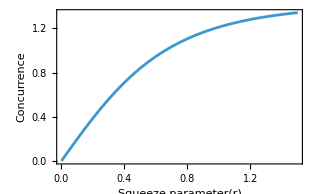

```mathematica
ListLinePlot[entanglementEntropies,Frame->True,FrameLabel->{"Squeeze parameter(r)","Concurrence"},LabelStyle->13]
```

For qudits the concurrence has a limit value of √(2(1-1/d)), for d=30 the upper bound is ≈ 1.39. We see we approach that value asymptotically when increasing r

### 7.7 Gaussian states

Gaussian states are a special subset of states of bosonic modes. Hamiltonians and processes in quantum optics that depend up to second order in the field operators preserve the property of a state being Gaussian. We will explore common gaussian states and their relation to quadratures and phase space calculations. In fact, we’ve already been working with gaussian states since Chapter 2.  The coherent states are Gaussian, which shouldn’t be much of a shock, given that their phase-space representation is a literal Gaussian function. A case more interesting is that the squeeze operator does not make a state lose its Gaussian class, because after acting on a state it can still be described by multivariate Gaussian function but with asymmetric variance scaling

Considering n bosonic modes with position and momentum operators or quadratures (using 1/√2 convention) (x̂)_k=((â)_k+(â)_k^†)/√2 and (p̂)_k=((â)_k-(â)_k^†)/ⅈ √2 fulfilling [(x̂)_k,(p̂)_l]=ⅈ δ_(k l) . A rotated quadrature operator is defined as x_k(ϕ)=1/(√2)((â)_k ⅇ^(-ⅈ ϕ)+(â)_k^†ⅇ^(ⅈ ϕ)) such that (x̂)_k(0)=(x̂)_k and (x̂)_k(π/2)=(p̂)_k

The rotated quadratures have the commutator [x_k(ϕ),x_l(φ)]=ⅈ  δ_(k l)sin(φ-ϕ)

Check for the same mode, k =l:

```mathematica
xOp[ϕ_]:=1/(√2)(a ⅇ^(-ⅈ ϕ)+SuperDagger[a] ⅇ^(ⅈ ϕ))
```

```mathematica
FullSimplify[NonCommutativePolynomialReduction[Commutator[xOp[ϕ],xOp[φ]],{Commutator[a,SuperDagger[a]]-1},{a,SuperDagger[a]},NonCommutativeAlgebra[{"ScalarVariables"->{ϕ,φ}}]]]
```

-ⅈ sin(ϕ-φ)

It is useful to define the 2 n quadrature operators as a column vector r̂={x_1,p_1,x_2,p_(2,)... , x_n, p_n}^T, such that commutation relations can be written as [(r̂)_k, (r̂)_l]= ⅈ Ω_(k,l)  where Ω is called the symplectic matrix Ω=⊕_(k =1)^(2n) (0 | 1
-1 | 0)= 𝟙_n⊗(0 | 1
-1 | 0)

Generator of the n-mode quadrature operators as a list:

```mathematica
rQuad[n_]:=BlockMap[Splice[{(#1⟦1⟧+#1⟦2⟧)/√2,(#1⟦1⟧-#1⟦2⟧)/(ⅈ √2)}]&,FieldVariables[a,Range[n]],2];
```

Definition of n-mode bosonic algebra:

```mathematica
nModeAlg[n_]:=With[{vars=FieldVariables[a,Range[n]]},NonCommutativeAlgebra[<|"Generators"->vars,"CommutationRelations"->BosonicRelations[vars]|>]]
```

Set up for n =3:

```mathematica
rs =rQuad[3]
alg = nModeAlg[3];
```

{(a1^†+a1)/(√2),-(ⅈ (a1-a1^†))/(√2),(a2^†+a2)/(√2),-(ⅈ (a2-a2^†))/(√2),(a3^†+a3)/(√2),-(ⅈ (a3-a3^†))/(√2)}

Generate all the possible commutators spanning a matrix:

```mathematica
commMat =Table[NonCommutativePolynomialReduction[Commutator[rs[[i]],rs[[j]]],alg["CommutationRelations"],alg],{i,6},{j,6}]
```

(0 | ⅈ | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | -ⅈ | 0)

Symplectic matrix for n-modes:

```mathematica
symplectic[n_]:=KroneckerProduct[IdentityMatrix[n],{{0,1},{-1,0}}]
```

Verify it is the same as the symplectic matrix for three modes:

```mathematica
ⅈ symplectic[3]==commMat
```

True

For a n-mode state the covariance matrix σ is defined as

σ_(k,l)=1/2(⟨{(r̂)_k,(r̂)_l}⟩-⟨(r̂)_k⟩⟨(r̂)_l⟩)   where {..} denotes anticommutator

their diagonal elements represent quadrature variances and the nonzero off-diagonal entries correspond to correlations between quadratures

The covariance matrix is real, symmetric , positive definite and σ+ⅈ/2 Ω≥0

Test for a single mode state numerically, we use CovarianceMatrix:

```mathematica
cov = CovarianceMatrix[QuantumState["RandomPure",$FockSize]]
```

{{5.1357,-0.81192},{-0.81192,6.75343}}

```mathematica
PositiveSemidefiniteMatrixQ[cov+ⅈ/2 sympletic[1]]
```

True

A state is said to be Gaussian if it is completely determined by the first and second moments of the quadrature operators, that is the expectation value of the quadrature vector r^—= ⟨r̂⟩ and the covariance matrix σ.

That is a direct analogue why a Gaussian(or normal) distribution is completely determined by the first two cumulants, the rest are 0

```mathematica
Cumulant[NormalDistribution[μ,σ],n]
```

Piecewise[{{μ, n==1}, {σ^2, n==2}, {0, True}}]

This has a straightforward implication in the phase space representation, the n-mode Wigner function can be represented as a multivariate Gaussian function:

W(r)=1/((2π)^n √(det(σ)))ⅇ^(-1/2(r-r^—)^T σ^-1(r- r^—))   such that  ∫_(ℝ^(2n)) W(r)=1

Wigner function implementation for a Gaussian state:

```mathematica
gaussianW[st_,{x_,p_}]:=Block[{cov,ms,v},
{cov,ms}=Values[CovarianceMatrix[st,"ReturnMeans"->True]];v={x,p}-ms;Exp[-1/2 v.cov.v]/((2 π)^(Length[ms]/2) √Det[cov])]
```

Calculate the numerical Wigner function for a squeezed vacuum state:

```mathematica
wig1 = WignerFunction[SqueezeOperator[0.3+0.2ⅈ,40][],{x,p}];
```

Also compute it with the function defined for Gaussian states:

```mathematica
wig2 =gaussianW[SqueezeOperator[0.3+0.2ⅈ,40][],{x,p}]//Chop//Simplify
```

0.31831 ⅇ^(-0.618095 p^2-0.871158 p x-1.92483 x^2)

Verify they are numerically the same for random phase space points:

```mathematica
Chop[(wig1-wig2)/.{x->#1,p->#2}&@@@RandomReal[{-4,4},{50,2}]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Gaussian operations

An operator of n-modes is defined to be a Gaussian operation if when passed a Gaussian state it returns back a Gaussian state (preserves the Gaussian status). Since Gaussian states can be described by r^— and σ, a Gaussian operation is characterized how it transforms r^— and σ. Unitary Gaussian operations can be generated if have at most quadratic dependence on (â)_k,(â)_k^†. They can be expressed with the following mappings, also called symplectic relations

σ->F σ F^T 
r^—-> F r^—+d         for d  2n vector and the matrix F satisfies F Ω F^T=Ω

Every Gaussian unitary has a symplectic transformation associated to it, and for all symplectic transformations there exists a Gaussian unitary that generates it.

Displacements

Given an n-mode state and the complex vector of displacement amplitudes α={α_1,α_2,… α_n} generated by D_1(α_1)⊗D_2(α_2)⊗… D_n(α_n), we get σ->σ, r^—=r^—+√2(Re(α_1), Im(α_1), Re(α_2),Im(α_2),…, Re(α_n), Im(α_n))

So F=1_(2n) and d= √2(Re(α_1), Im(α_1), Re(α_2),Im(α_2),…, Re(α_n), Im(α_n))

Define two random complex amplitudes:

```mathematica
{α1,α2}= RandomComplex[{0.5+0.5ⅈ},2];
```

Define a two mode state:

```mathematica
s= FockState[{3,2}];
```

Calculate σ and also return the means vector:

```mathematica
TraditionalForm/@CovarianceMatrix[s,"ReturnMeans"->True]
```

<|CovarianceMatrix→(7/2 | 0 | 0 | 0
0 | 7/2 | 0 | 0
0 | 0 | 5/2 | 0
0 | 0 | 0 | 5/2),Means→{0,0,0,0}|>

Compute the same quantities after applying the displacements:

```mathematica
cov =CovarianceMatrix[DisplacementOperator[α1,{1}]@DisplacementOperator[α2,{2}]@s,"ReturnMeans"->True];
```

Indeed σ is unchanged:

```mathematica
RootApproximant@Chop@cov["CovarianceMatrix"]
```

(7/2 | 0 | 0 | 0
0 | 7/2 | 0 | 0
0 | 0 | 5/2 | 0
0 | 0 | 0 | 5/2)

And the modified means vector has the expected form:

```mathematica
Chop[Flatten[√2 ReIm/@{α1,α2}]-cov["Means"]]
```

{0,0,0,0}

Phase shifts

The phase shift or phase space rotation that we saw in Chapter 3 transforms the mode operator as â->ⅇ^(-ⅈ ϕ)â.  And the quadratures transform as x̂->x̂(ϕ), p̂->x̂(ϕ+π/2).  For phase shifts F=(cos(ϕ) | sin(ϕ)
-sin(ϕ) | cos(ϕ))=R(ϕ) and d=0

Let’s verify that with a simple superposition state:

```mathematica
ψ = 1/(√2)(FockState[3]+FockState[5]);
```

Calculate σ and r^—:

```mathematica
cov =FullSimplify/@CovarianceMatrix[ψ,"ReturnMeans"->True]
```

<|CovarianceMatrix→{{9/2+√5,0},{0,9/2-√5}},Means→{0,0}|>

Since r^—=0 and d=0, r^— will remain unchanged

Calculate σ after applying the phase shift:

```mathematica
FullSimplify[CovarianceMatrix[PhaseShiftOperator[θ]@ψ],θ ∈Reals]
```

(√5 cos(2 θ)+9/2 | √5 sin(2 θ)
√5 sin(2 θ) | 9/2-√5 cos(2 θ))

Verify the symplectic relation:

```mathematica
With[{F=RotationMatrix[θ]},Simplify[F.cov["CovarianceMatrix"].Fᵀ]]
```

(√5 cos(2 θ)+9/2 | √5 sin(2 θ)
√5 sin(2 θ) | 9/2-√5 cos(2 θ))

Single mode squeezing

We saw in a previous section how the single mode squeeze operator S(ξ) (ξ=r ⅇ^(ⅈ θ)) transforms the field operators. Given this it’s possible to derive how the quadratures are transformed, so we can get the symplectic relations

F=cosh(r)𝟙_2+sinh(r)S_θ=F_ξ    with S_θ=(cos(θ) | sin(θ)
sin(θ) | -cos(θ))
d = 0

When multiple single-mode squeeze operators are applied to different modes with parameters ξ_1,ξ_2... ξ_n, then F=⊕_(k=1)^n F_ξ_k, d=0

Define the complex squeezing value:

```mathematica
ξ=RandomReal[{0,0.2}] ⅇ^(ⅈ RandomReal[{0,2π}]);
```

Covariance matrix of the vacuum:

```mathematica
covs =Chop/@ CovarianceMatrix[FockState[0],"ReturnMeans"->True]
```

<|CovarianceMatrix→{{1/2,0},{0,1/2}},Means→{0,0}|>

And for the squeezed vacuum:

```mathematica
sqCovs =CovarianceMatrix[SqueezeOperator[ξ][],"ReturnMeans"->True]
```

<|CovarianceMatrix→{{0.434984,-0.0116824},{-0.0116824,0.575048}},Means→{0.,0.}|>

Calculate it using the symplectic relation of squeezing:

```mathematica
Block[{r=Abs[ξ],θ=Arg[ξ],F},F=Cosh[r] IdentityMatrix[2]-Sinh[r] ({{cos(θ), sin(θ)}, {sin(θ), -cos(θ)}});
F.covs["CovarianceMatrix"].Fᵀ]
```

{{0.434984,-0.0116824},{-0.0116824,0.575048}}

Assert the equality numerically:

```mathematica
%==sqCovs["CovarianceMatrix"]
```

True

Two mode squeezing

In section 7.6 we saw how the two mode squeeze operator transforms the field operators. Using those relations it is possible to derive how the quadratures transform, lets perform that calculation

Define back-substitution rules:

```mathematica
quadRules = {a1->(x1+ⅈ p1)/(√2),SuperDagger[a1]->(x1-ⅈ p1)/(√2),a2->(x2+ⅈ p2)/(√2),SuperDagger[a2]->(x2-ⅈ p2)/(√2)};
```

Transform the quadratures using the vector {x_1, p_1,x_2,p_2}:

```mathematica
transformQuadratures =BosonicExpSimplify[S2[-r ⅇ^(ⅈ θ)]**(#)**S2[r ⅇ^(ⅈ θ)],Assumptions->θ∈Reals &&r>0]&/@rQuad[2];
```

Show the simplified transformed quadratures:

```mathematica
FullSimplify[transformQuadratures/.quadRules]//Expand
```

{x1 Cosh[r]-x2 Cos[θ] Sinh[r]-p2 Sin[θ] Sinh[r],p1 Cosh[r]+p2 Cos[θ] Sinh[r]-x2 Sin[θ] Sinh[r],x2 Cosh[r]-x1 Cos[θ] Sinh[r]-p1 Sin[θ] Sinh[r],p2 Cosh[r]+p1 Cos[θ] Sinh[r]-x1 Sin[θ] Sinh[r]}

From this the symplectic relations can be computed:

F=(cosh(r)𝟙_2 | -sinh(r)S_θ
-sinh(r)S_θ | cosh(r)𝟙_2)≡ F_(2, ξ)         d=0

where S_θ has the same meaning as before

When acting on a pair of modes (say i, j) of an n-mode system, the symplectic matrix should be equal to F_(2,ξ) in the i j-subspace and identity on the rest

Controlled phase

It is defined as CZ(ϕ)= ⅇ^(ⅈ ϕ x_1 x_2), let’s explore how the quadratures transform. This represents a controlled operation based on position, let’s derive how the quadratures change

Define the controlled phase:

```mathematica
CZ[ϕ_]:=Exp[ⅈ ϕ ((a1+SuperDagger[a1])/(√2))**((a2+SuperDagger[a2])/(√2))]
```

Show the transformations, momentum quadratures get shifted based on the position of the other mode:

```mathematica
BosonicExpSimplify[CZ[-ϕ]**(#)**CZ[ϕ]]&/@rQuad[2]/.quadRules//Simplify//Column
```

x1
p1+x2 ϕ
x2
p2+x1 ϕ

So we get:

F=(1 | 0 | 0 | 0
0 | 1 | ϕ | 0
0 | 0 | 1 | 0
ϕ | 0 | 0 | 1),   d=0

There are other operations that can be proven to be Gaussian like tracing out a mode, homodyne measurements, vacuum and Gaussian projections, etc

#### Examples of Gaussian states

We will now mention widely used Gaussian states along with their σ and r⃗.  The presented states all  were studied in this chapter and the previous ones. They are single and two mode states, however, the extension when having a product state of more modes can be easily done with direct sum of covariance matrices and displacement vector join

Vacuum state

Is the ground state of the quantum harmonic oscillator has σ=1/2 I_2 and r^—=0

```mathematica
Dataset[MatrixForm/@CovarianceMatrix[FockState[0],"ReturnMeans"->True]]
```

Coherent state

We have used this state Gaussian state a lot, using that |α⟩ =D(α)|0⟩ is easy to show that:

```mathematica
Dataset[TraditionalForm@*MatrixForm/@<|"CovarianceMatrix"->{{1/2,0},{0,1/2}},"Means"->{√2 Re[α],√2 Im[α]}|>]
```

Thermal state

The canonical thermal state of a single bosonic mode has σ=(n^—+1/2)I_2 and r^—=0

Check for n^—=1:

```mathematica
Dataset[MatrixForm/@N@CovarianceMatrix[ThermalState[1,40],"ReturnMeans"->True]]
```

Of course for states that have an infinite representation in Fock space, the results are approximate and dependent on cutoff

Single mode squeezed vacuum

Given that |ξ⟩ = S(ξ) |0⟩ with ξ=r ⅇ^(ⅈ θ), we can use the symplectic transformation to get σ and r^—

```mathematica
Dataset[<|"CovarianceMatrix"->TraditionalForm[1/2 Cosh[2r]SymbolicOnesArray[2]-1/2 Sinh[2r] Subscript[S, θ]],"Means"->{0,0}|>]
```

Two mode squeezed vacuum

In a very similar way |ξ_(2-mode)⟩=S_2(ξ)|00⟩, so we obtain for σ and r^—

```mathematica
Grid[KeyValueMap[{Item[Style[#1,GrayLevel[0.2]],Background->GrayLevel[0.94],Alignment->Left],Replace[#2,m_?MatrixQ:>MatrixForm[m]]}&,<|"CovarianceMatrix"->TraditionalForm[{{1/2 Cosh[2 r] SymbolicOnesArray[2],-(1/2) Sinh[2 r] Subscript[S,θ]},{-(1/2) Sinh[2 r] Subscript[S,θ],1/2 Cosh[2 r] SymbolicOnesArray[2]}}],"Means"->{0,0,0,0}|>],Frame->All,FrameStyle->GrayLevel[0.85],Alignment->{Left,Center},Spacings->{1.4,1.1},BaseStyle->{FontFamily->"Source Sans Pro",FontSize->14}]
```

CovarianceMatrix | (1/2 2 cosh(2 r) | -1/2 sinh(2 r) S_θ
-1/2 sinh(2 r) S_θ | 1/2 2 cosh(2 r))
Means | {0,0,0,0}

Initialization

Load the Quantum Framework:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load the second quantization tools:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Useful definitions:

```mathematica
a := AnnihilationOperator[]
```

```mathematica
formattedExpr=;
```

Vocabulary

SqueezeOperator |   | represents a quantum operator that applies squeezing to any 
single mode state
CatState |   | defines a  Schrodinger cat state with arbitrary amplitude and phase

Exercises

Load the Quantum Framework paclet:

Needs["Wolfram`QuantumFramework`"]
Needs["Wolfram`QuantumFramework`SecondQuantization`"]

Applying on a coherent state with the annihilation operator has no effect on the state itself.04. But consider now the effect of operating on a coherent state with the creation operator a^†. Obtain the normalized state and investigate its properties. Is it a nonclassical state? Check the negative area of the Wigner function varying the value α of the coherent state.

Solution

Calculate the Wigner representation for α = 0.5:

s = a^†@CoherentState[][0.5];
wig = WignerRepresentation[s,{-6,6},{-6,6}];

Show the plot:

DensityPlot[wig[x,p],{x,-6,6},{p,-6,6},PlotRange->All,PlotPoints->100,ColorFunction->"Rainbow",PlotLegends->Automatic,FrameLabel->{"x","p"}]

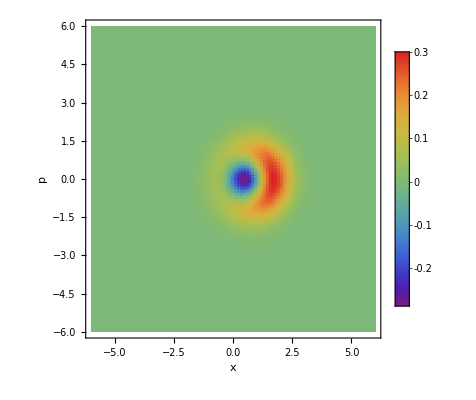

Negative area can be calculated as ∫∫  |W(x,p)| dx dp - 1:

negativeAreas=Table[s = (a^†@CoherentState[][α])["Normalize"];wig = WignerRepresentation[s,{-6,6},{-6,6}];{α,NIntegrate[Abs[wig[x,p]],{x,-6,6},{p,-6,6}]-1},{α,0,1.5,0.1}]//Quiet;

We see there is a negative area but it decreases as α increases, a coherent state with bigger values of α is more “classical”

ListLinePlot[negativeAreas,InterpolationOrder->2,AxesLabel->{"α","Negative Area"}]

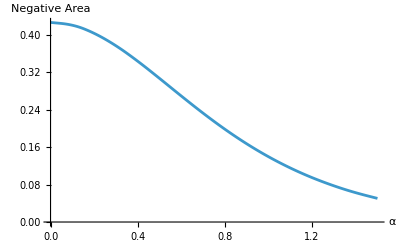

Consider the operators defined as 
K_1 = 1/2 ((a^†)^2+a^2) ,  K_2=1/2ⅈ ((a^†)^2-a^2),  K_3 = 1/2 (a^†a+1/2)
The first two are sometimes referred to as the quadratures of the square of the field. Show that these operators form a closed set under commutation,that is, the commutator of any two yields the third (up to proportionality constant). Obtain the uncertainty product for the operators K1 and K2 and use the coherent states |α⟩.04 to see if they equalize this product.

Solution

Define the operators:

K1 = 1/2(a^†**a^†+a**a);
K2 = 1/(2ⅈ)(a^†**a^†-a**a);
K3 = 1/2(a^†**a+1/2);

Define the variables and the commutation relation:

vars = {a,a^†};
commRel ={Commutator[a,a^†]-1};

Show [K_1,K_2] = -4 ⅈ K_3:

NonCommutativePolynomialReduce[Commutator[K1,K2]+4ⅈ K3,commRel,vars][[-1]]

0

Show  [K_2,K_3] =  ⅈ K_1:

NonCommutativePolynomialReduce[Commutator[K2,K3]-ⅈ K1,commRel,vars][[-1]]

0

Show [K_3,K_1] =  ⅈ K_2:

NonCommutativePolynomialReduce[Commutator[K3,K1]-ⅈ K2,commRel,vars][[-1]]

0

Using the uncertainty principle for two operators A and B we have ΔA ΔB ≥ 1/2| ⟨ [ A, B] ⟩ |, applying to this case we get Δ K_1 ΔK_2 ≥ 2 ⟨ K_3⟩

Defining as quantum operators:

K1op = 1/2((a^†)^2+a^2);
K2op = 1/(2ⅈ)((a^†)^2-a^2);
K3op = 1/2(a^†@a+1/2);

Random complex amplitude:

αcoh = RandomReal[{0,2}];

Evaluate the left and right hand side of the inequality:

LHS =√(OperatorVariance[CoherentState[][αcoh],K1op]OperatorVariance[CoherentState[][αcoh],K2op]);

RHS = 2((CoherentState[][αcoh])^†@K3op@CoherentState[][αcoh])["Scalar"];

We see it satisfies the equality:

Chop[LHS-RHS]

0

Examine numerically the m-photon added Yurke-Stoler. Discuss photon distribution and phase space behavior of the states for α=0.25 and α =2 and m=1,2

Solution

SetFockSpaceSize[40];
a := AnnihilationOperator[]

Generate the photon added states for m=0,1,2:

{states025,states2}=Table[With[{s=CatState[][α,π/2]},{s,a^†[s]["Normalize"],(a^†)^2[s]["Normalize"]}],{α,{0.25,2.}}];

After adding photons, the Yurke-Stoler state always becomes sub-Poissonian:

MandelQParameter/@states025//Chop

{0,-0.894889,-0.923162}

MandelQParameter/@states2//Chop

{0,-0.282759,-0.411765}

Compute the WignerRepresentation for all the states:

wigFuncs = WignerRepresentation[#,{-5,5},{-5,5}]&/@Join[states025,states2];

Visualize W(x,p) for α = 0.25:

Legended[GraphicsRow[(DensityPlot[#1[x,p],{x,-5,5},{p,-5,5},]&)/@wigFuncs⟦1;;3⟧],]

-Graphics-

Visualize W(x,p) for α = 2:

Legended[GraphicsRow[(DensityPlot[#1[x,p],{x,-5,5},{p,-5,5},]&)/@wigFuncs⟦4;;6⟧],]

-Graphics-

Photon adding modifies the phase-space structure and the parity, an odd number of added photons produces a phase shift of π respect to the original state. When α increases we can also see its effect on the interference fringes of the Wigner function

Of course the Wigner functions of the photon added states for m=1 and m=2 have to be orthogonal (up to numerical and truncation errors):

NIntegrate[wigFuncs[[5]][x,p]wigFuncs[[6]][x,p],{x,-5,5},{p,-5,5},Method->"LocalAdaptive"]

0.000557355

Based on the procedure for transforming the quadratures under  two mode squeezing, prove the squeezed EPR correlations regarding position and momentum. Hint: What angle is really convenient to use?

Solution

Use the previous definitions:

quadRules = {a1->(x1+ⅈ p1)/(√2),a1^†->(x1-ⅈ p1)/(√2),a2->(x2+ⅈ p2)/(√2),a2^†->(x2-ⅈ p2)/(√2)};

rQuad[n_]:=BlockMap[Splice[{(#1⟦1⟧+#1⟦2⟧)/(√2),(#1⟦1⟧-#1⟦2⟧)/(ⅈ √2)}]&,FieldVariables[a,Range[n]],2]

S2[ξ_]:=Exp[Conjugate[ξ] a1**a2-ξ a1^†**a2^†]

The convenient angle is θ=0, so we can call the operator with just the squeezing magnitude:

transformQuadratures =BosonicExpSimplify[S2[-r ]**(#)**S2[r ],Assumptions->r>0]&/@rQuad[2];

Simplified transformed quadratures:

xp=FullSimplify[transformQuadratures/.quadRules];

We show squeezing and “anti-squeezing” for sum and difference of the quadratures:

FullSimplify[Join[xp[[1;;2]]+xp[[3;;4]],xp[[1;;2]]-xp[[3;;4]]]]//Column

(x1+x2) ⅇ^-r
(p1+p2) ⅇ^r
(x1-x2) ⅇ^r
(p1-p2) ⅇ^-r

References

Gerry,Christopher C.,and Peter L.Knight.Introductory Quantum Optics. Cambridge:Cambridge University Press,2005.

Walls, D. F., and Gerard J. Milburn. Quantum Optics. 2nd ed. Berlin: Springer, 2008.

Dodonov, Vladimir V., and Valerii I. Man’ko. Theory of Nonclassical States of Light. London: Taylor & Francis, 2003.

Schleich, Wolfgang P. Quantum Optics in Phase Space. Berlin: Wiley-VCH, 2001.

Vogel, Werner, and Dirk-Gunnar Welsch. Quantum Optics. 3rd ed. Weinheim: Wiley-VCH, 2006.

Teich, M. C., and B. E. A. Saleh. Squeezed States of Light. Quantum Optics: Journal of the European Physical Society B 1, no. 3 (1989): 153-191

Scully, Marlan O., and M. Suhail Zubairy. Quantum Optics. Cambridge: Cambridge University Press, 1997.

Weedbrook, Christian, Stefano Pirandola, Raúl García-Patrón, Nicolas J. Cerf, Timothy C. Ralph, Jeffrey H. Shapiro, and Seth Lloyd. Gaussian Quantum Information. Reviews of Modern Physics 84, no. 2 (2012): 621–69.

Bužek, V., A. Vidiella-Barranco, and Peter L. Knight. Superpositions of coherent states: Squeezing and dissipation. Physical Review A 45, no. 9 (1992): 6570.

Yurke, Bernard, and David Stoler. “Generating quantum mechanical superpositions of macroscopically distinguishable states via amplitude dispersion.” Physical review letters 57, no. 1 (1986): 13.